```mathematica
ClearAll["Global`*"]
```

```mathematica
DispersionRelationship[k_,κ1_,κ2_,m_,a_]:=Sqrt[(2κ1)/m(1-Cos[k a])+(2κ2)/m(1-Cos[2k a])];
```

```mathematica
k1=100;
k2=1;
(*m=9.109*^-31;*)
m=1;
aCte=1;
```

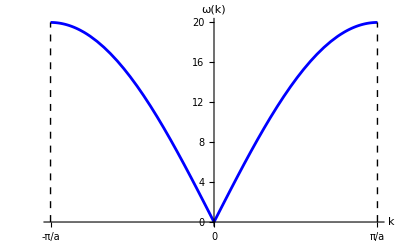

```mathematica
Plot[DispersionRelationship[x,k1,k2,m,aCte],{x,-π/aCte,π/aCte},AxesLabel->{k,"ω(k)"},
Ticks->{{{-π/aCte,-π/a}, {0,0},{π/aCte,π/a}}, None},
Epilog->{{Dashed,Line[{{π,0},{π,DispersionRelationship[π,k1,k2,m,aCte]}}]},
{Dashed,
Line[
{{-π,0},{-π,DispersionRelationship[-π,k1,k2,m,aCte]}}
]}
},
TicksStyle->Directive[Black,8.5],PlotStyle->Blue,
BaseStyle->{FontFamily-> "CMU Classical Serif",FontSize->11, FontWeight->Bold}]
```

```mathematica
Export[NotebookDirectory[]<>"./img/FirstBrillouinZone.pdf",%,ImageResolution-> 2000];
```

```mathematica
Export[NotebookDirectory[]<>"./img/FirstBrillouinZone.png",%,ImageResolution-> 2000];
```